```mathematica
p=Normal@Series[ComplexExpand[1/Abs@(Subscript[b, 0]+Subscript[b, 1] ϕ+Subscript[b, 2] ϕ^2), {Subscript[b, 0], Subscript[b, 1], Subscript[b, 2]}], {ϕ, 0, 2}]/.{ϕ->√(Γ/Re[Subscript[b, 1]])x};
noExp = Normal@Series[Exp[(-Re[Subscript[b, 2]/6] ϕ^3-Re[Subscript[b, 3]/24] ϕ^4)/Γ]/.{ϕ->√(Γ/Re[Subscript[b, 1]])x}, {Γ, 0, 1}];
newpol = CoefficientList[Normal@Series[noExp * p,  {Γ, 0, 1}], x];
intmonom = Table[Assuming[kk>0,Integrate[Exp[-x^2 - I kk x] x^(n-1), {x, -Infinity, Infinity}]], {n, 7}];
res=Normal@Series[Total[(newpol*intmonom)/(ⅇ^(-kk^2/4))/.{kk->k*√(Γ/Re[Subscript[b, 1]])}], {Γ, 0, 1}];
b2=I^2/(1-I Rs)^3(w-2 w^2)/.{w->-I Rs};
b3=I^3/(1-I Rs)^5(-5 w(w-2 w^2)+(w+w^2)(w-2 w^2))/.{w->-I Rs};
rules={Subscript[b, 0]->1-I Rs, Subscript[b, 1]->Rs/(1-I Rs), Subscript[b, 2]->b2, Subscript[b, 3]-> b3};
ress=res/.rules//ComplexExpand;
akaAk = Total[(CoefficientList[Normal@Series[ress//Simplify, {Γ, 0, 1}], Γ]//Simplify)*{1, Γ}];
{A0, A1}=CoefficientList[akaAk, k]/{1, 2I Γ}
```

{(√π)/(√(1+Rs^2))+(√π Rs (503-1142 Rs^2-49 Rs^4+12 Rs^6) Γ)/(192 (1+Rs^2)^(7/2)),(√π (-1+3 Rs^2))/(16 (1+Rs^2)^(3/2))}

{(√π)/(√(1+Rs^2))+(503 √π Rs Γ)/(192 (1+Rs^2)^(7/2))-(571 √π Rs^3 Γ)/(96 (1+Rs^2)^(7/2))-(49 √π Rs^5 Γ)/(192 (1+Rs^2)^(7/2))+(√π Rs^7 Γ)/(16 (1+Rs^2)^(7/2)),(ⅈ √π (-1+3 Rs^2) Γ)/(8 (1+Rs^2)^(3/2)),-(√π √(1+Rs^2) Γ)/(4 Rs)}

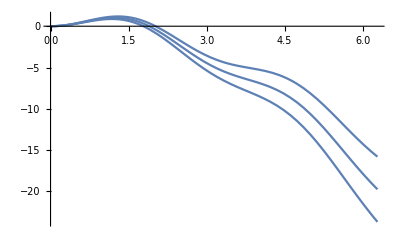

```mathematica
Plot[Table[1-Cos[2x] - χ x^2, {χ, 0.4, 0.6, 0.1}], {x, 0, 2π}]
```

```mathematica
Sum[x^(2n)/(n!(n+k)!), {n, 0, Infinity}]
```

x^-k BesselI[k,2 x]

-BesselI[-k,2 x]+BesselI[k,2 x]

125.664

{62.8319,125.664,188.496,251.327,314.159}

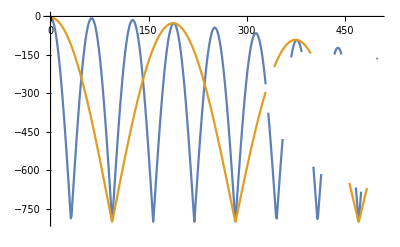

```mathematica
Γ = 0.05;
A=10*2/Γ;
(2π)/Γ
krange ={0, 500};
(*T1 = Table[{k,Log@Abs@(BesselI[k, 2A Exp[I k Γ]])+(A/2*Re@(1-Exp[2I k Γ])-2A)}, {k, krange[[1]], krange[[2]]}];*)
(*T2 = Table[{k,Log@Abs@(BesselI[k, 2A Exp[I k Γ]])-2A}, {k, krange[[1]], krange[[2]]}]*)
T3 = Table[{k,Log@Abs@(BesselI[k, 2A Exp[I k Γ]])-2A}, {k, krange[[1]], krange[[2]]}];
T4 = Table[{k,Log@Abs@(BesselI[k, 2A Exp[I k Γ/3]])-2A}, {k, krange[[1]], krange[[2]]}];
π/Γ*Range[5]
n=300;
t1 = Table[{(2π)/n j,Log@Abs@(BesselI[100, 2A Exp[I (2π)/n j]]) },{j, 1, n}];
t2 = Table[{(2π)/n j,Log@Abs@(BesselI[3, 2A Exp[I (2π)/n j]]) },{j, 1, n}];
t3 = Table[{(2π)/n j,Log@Abs@(BesselI[2, 2A Exp[I (2π)/n j]]) - Log@Abs@(BesselI[3, 2A Exp[I (2π)/n j]]) },{j, 1, n}];
ListPlot[{T3, T4}, Joined->True]
```

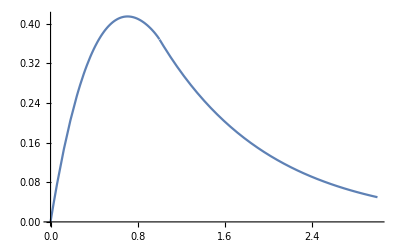

```mathematica
Clear[t]
f[z_, t_]=(z t Exp[√(1-(z t)^2) -z/4(1-t^2)-z ])/(1+√(1-(z t)^2));
Plot[Abs@f[z, -1], {z, 0, 3}]
(*ContourPlot[Abs@f[Abs[x+I y], Exp[I Arg[x+I y]]]==0.41, {x, -2, 2}, {y, -1, 1}]*)
```

```mathematica
Assuming[{a>0},Integrate[4 r Exp[-2(r-a)^2-4 a r]BesselI[0,4r a] , {r, 0, Infinity}]]
```

1

-x^4/2+O[x]^5

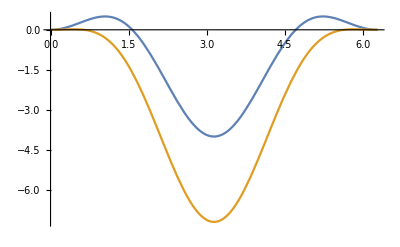

```mathematica
Series[1-Cos[2x] - 4(1-Cos[x]), {x, 0, 4}]
Plot[{1-Cos[2x] -4*0.5(1-Cos[x]),1-Cos[2x] - 4*0.9(1-Cos[x])}, {x, 0, 2π}]
```

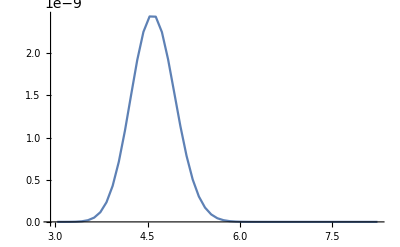

```mathematica
{a, Γ, ϕ} = {8, 10^-2, 0.03};
kmax=100;
t=Table[{r,2/π Exp[-2(r-a)^2]Re@Sum[BesselI[k, 4 a r Exp[I k Γ]]Exp[I k ϕ]Exp[a^2(1-Exp[2I k Γ])-4 a r], {k, -kmax, kmax}]}, {r, a-3/2 √a, a+√a/2, 0.1} ];
ListPlot[t, Joined->True]
```

316.228

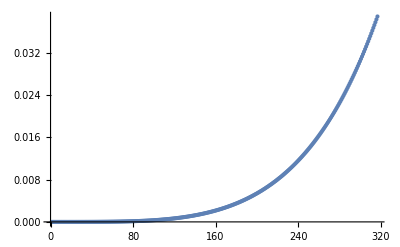

```mathematica
A=100000;
√A//N
t=Abs@Table[{k,BesselI[k, 2A](Exp[ 2A]/(√(2π 2A))(1+(4 k^2-1)/(4(-2*2A))))^-1-1}, {k,1, Ceiling[√A]}] ;
ListPlot[t]
```

```mathematica
1
```

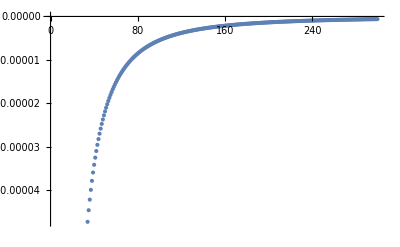

```mathematica
z=2Exp[I];
t1=Table[{n,-Log@Abs[BesselI[n, n^2 z]((Exp[n^2 z]Exp[-1/(2z)])/(√(2π n^2 z)))^-1]}, {n, 1, 300}];

(*z=.
t2=Table[Log[BesselI[n, n^2 z](Exp[n^2 z]/Sqrt[2π n^2 z  ])^-1]/.{n->200}, {z, 0.5, 2, 0.1}];*)
ListPlot[t1]
```

{201}

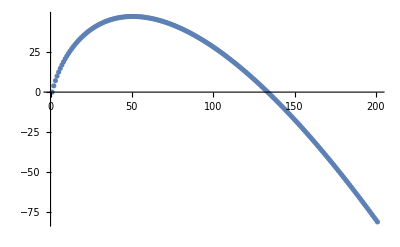

```mathematica
k=10^4;
z=10^6;
t=Table[Log[Abs@(Gamma[k+m+1/2]/(m!Gamma[k-m+1/2]))(2z)^-m],{m,0, 200, 1}];
Ordering[t, -1]
ListPlot[t]
```

```mathematica
k=.
Gamma[k+m+1/2]/(m!Gamma[k-m+1/2])/.{m->k^2 t};
Assuming[{t>0, Element[t k^2, Integers]},Series[Gamma[1/2+k+k^2 t]/((k^2 t)! Gamma[1/2+k-k^2 t](k^2 t)^(k^2 t)), {k ,Infinity, 3}]]//Simplify
```

ⅇ^(-t k^2+(-2 Log[k]-Log[t]+Log[k^2 t]) k+1/(2 t)+O[1/k]^1) Cos[k π (-1+k t)] ((ⅇ^(1/2/t) √(2/π))/(√t k)+O[1/k]^2)

```mathematica
Limit[Gamma[k+m+1/2]/(m!Gamma[k-m+1/2] k^(2m)), k->Infinity]
```

1/(m!)

```mathematica
Sum[m(4 m^2-1)/(m!)(-t)^m, {m, 0, Infinity}]
```

-ⅇ^-t t (3-12 t+4 t^2)

```mathematica
v=Simplify[Exp[t]Normal@Series[Sum[Normal[Series[Gamma[k+m+1/2]/(m! Gamma[k-m+1/2] k^(2m)), {k, Infinity, 6}]//Simplify](-t)^m, {m, 0, Infinity}], {k, Infinity, 6}]];
v/.{t->k^2/(2z)}
```

1+(k^18/(82944 z^9)-(17 k^16)/(23040 z^8)+(4943 k^14)/(322560 z^7)-(1513 k^12)/(11520 z^6)+(1381 k^10)/(3072 z^5)-(751 k^8)/(1536 z^4)+(75 k^6)/(1024 z^3))/k^6+(405+(5 k^8)/z^4-(132 k^6)/z^3+(930 k^4)/z^2-(1740 k^2)/z)/(5760 z^2)+(3+k^4/z^2-(6 k^2)/z)/(24 z)

```mathematica
smax=6;
v=Range[smax+1];
For[s=0, s<=smax, s++,
ass= Normal@Simplify@Series[Gamma[k+m+1/2]/(Gamma[k-m+1/2] k^(2m)), {k, Infinity, 2*s}];
l=Limit[(CoefficientList[ass/.{k->r^(-1/2)},r][[s+1]])/m^(3s),m->Infinity];
v[[s+1]]=l]
```

```mathematica
Series[Log[Total[v*x^(Range[smax+1]-1)]], {x, 0, 6}]
v
CoefficientList[Normal@Series[Exp[-x/3],{x,0, smax}],x]
```

-x/3+O[x]^7

{1,-1/3,1/18,-1/162,1/1944,-1/29160,1/524880}

{1,-1/3,1/18,-1/162,1/1944,-1/29160,1/524880}

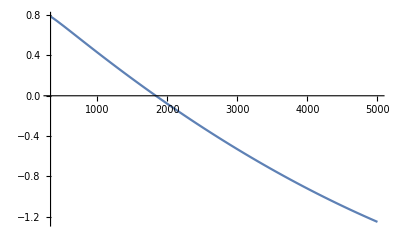

```mathematica
n=100;
Plot[Log[BesselI[n, z](Exp[z]/Sqrt[2π z] Exp[-n^2/(2z)])^-1]*(24 z^3)/n^4, {z,n^(4/3)/1.4, n^2/2}]
```

5623.41

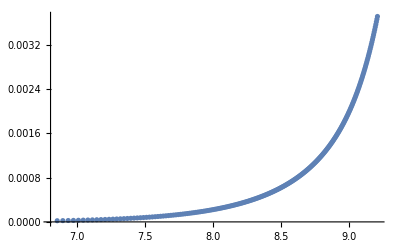

```mathematica
z=10^5;
t=Table[{Log[k],v=(-Log@(BesselI[k, z](Exp[z-k^2/(2z)+k^4/(24 z^3)]/Sqrt[2π z])^-1))},{k, Floor[3 z^(1/2)],Floor[z^(4/5)], 40}];
z^(3/4)//N
ListPlot[t]
```

```mathematica
t=ArcCos[β/α];
v=α^2(1-Cos[2t])-4α β(1-Cos[t])//TrigToExp//FullSimplify;
Series[v/.{β->α+d}, {d, 0, 6}]
```

2 d^2+O[d]^7

```mathematica
Table[l=m^2; l+1,{m,0,1}]
```

{1,2}

```mathematica
(1-Exp[2I x])a^2 - 4a (a+d)(1-Exp[I x])-2 d^2 +2 a^2((a+d)/a-Cos[x])^2-2I a^2( (2 (a+d)/a- Cos[x]) Sin[x])//FullSimplify
```

0

```mathematica
Series[ArcCos[1-x], {x, 0, 3}]
```

√2 √x+x^(3/2)/(6 √2)+(3 x^(5/2))/(80 √2)+O[x]^(7/2)

```mathematica
zk=4 α (α+δ) Exp[- I k Γ];
Series[D[Sqrt[zk^2+k^2]-k ArcSinh[k/zk]-α^2 Exp[-2I k Γ], k], {α, Infinity,0 }]
```

(2 ⅈ ⅇ^(-2 ⅈ k Γ) (-2 α^2+√(ⅇ^(-2 ⅈ k Γ) α^4)) Γ α^2)/(√(ⅇ^(-2 ⅈ k Γ) α^4))-(4 ⅈ ⅇ^(-2 ⅈ k Γ) α^2 Γ δ α)/(√(ⅇ^(-2 ⅈ k Γ) α^4))+O[1/α]^1

```mathematica
D[zk-k^2/(2zk)-α^2 Exp[-2I k Γ], k]==0//Simplify
```

(ⅇ^(2 ⅈ k Γ) k (-2 ⅈ+k Γ))/(α (α+δ))+32 α Γ (α+δ)==16 ⅇ^(-ⅈ k Γ) α^2 Γ

# Расчёт в окрестности пика по k при K=0

f это функция логарифма модуля слагаемого из ряда Фурье

```mathematica
ruleβ = β->α-d;
rulezk=zk->4 α β Exp[-I k Γ];
f=√(zk^2+k^2)-k ArcSinh[k/zk]-α^2 Exp[-2I k Γ];
```

```mathematica
derf = Assuming[{zk>0},Simplify[D[f/.zk->z[k], k]/.z'[k]->-I Γ z[k]/.z[k]->zk]];
derfAsymptotic =Series[derf, {zk, Infinity, 2}]//Normal;
nearK0=Series[ComplexExpand@Re[derfAsymptotic/.rulezk], {k, 0, 5}]//Normal 
(*В последнем выражении если учитывать больше слагаемых, то получится превышение точности выше 1. Если учитывать меньше, то это повлияет на поправки, вносящие существенный вклад*)
temp = nearK0/k;
kmaxSquared=Series[Simplify[k^2/.Solve[temp==0, k][[2,1]]]/.ruleβ, {α , Infinity, 4}]//Normal;
tmax =Assuming[{α>0, Γ>0}, Simplify[Series[Sqrt[kmaxSquared * Γ^2], {α, +Infinity, 2}]//Normal]]//Expand;
kmax = tmax/Γ
```

k (-1/(4 α β)+4 α^2 Γ^2-4 α β Γ^2)+k^3 (Γ^2/(4 α β)-(8 α^2 Γ^4)/3+2/3 α β Γ^4)+k^5 (-Γ^4/(32 α β)+(8 α^2 Γ^6)/15-1/30 α β Γ^6)

(d^(3/2)/(6 √2 α^(3/2))+(√2 √d)/(√α))/Γ

```mathematica
(*Предыдущая ячейка решалась слишком долго, поэтому продолжим в этой*)
kmax=(d^(3/2)/(6 √2 α^(3/2))+(√2 √d)/(√α))/Γ;
der2f = Assuming[{zk>0},Simplify[D[f/.zk->z[k], {k, 2}]/.{z'[k]->-I Γ z[k], z''[k]->-Γ^2 z[k]}/.z[k]->zk]]
```

4 ⅇ^(-2 ⅈ k Γ) α^2 Γ^2+(-1-2 ⅈ k Γ-zk^2 Γ^2)/(√(k^2+zk^2))

-1/(4 α β)+4 α^2 Γ^2-4 α β Γ^2

-1/(4 α^2)-4 α^2 Γ^2+4 β^2 Γ^2+(√(1-β^2/α^2) ArcCos[β/α])/(2 α β)+ArcCos[β/α]^2/(8 α^2)

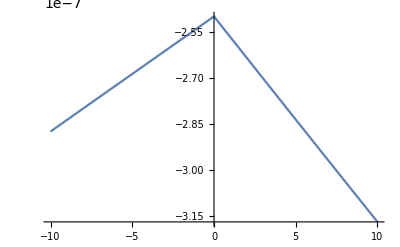

```mathematica
Assuming[{α>0, β>0},ComplexExpand[Re[der2f/.rulezk]]];
der2fAs = ComplexExpand[Re@Normal[Series[der2f, {zk, Infinity, 1}]]/.rulezk];
der2f0=der2fAs/.k->0//Simplify//Expand
der2fnot0=der2fAs/.k->1/Γ ArcCos[β/α]//Simplify//Expand
(* Проверка того, что оценки имеют непрерывную склейку*)
Plot[If[d>0,der2fnot0, der2f0]/.{β->α-d}/.{Γ->10^-6,α->1000},{d, -10, 10}]
```

```mathematica
(*Для упрощения в проге*)
((√(1-β^2/α^2) ArcCos[β/α])/(2 α β)+ArcCos[β/α]^2/(8 α^2))*8(α β)/ArcCos[β/α]//Simplify
```

4 √(1-β^2/α^2)+(β ArcCos[β/α])/α

# Насколько велик пик при K=1

-4 R^2-√(π^2+16 R^4)-π ArcSinh[π/(4 R^2)]

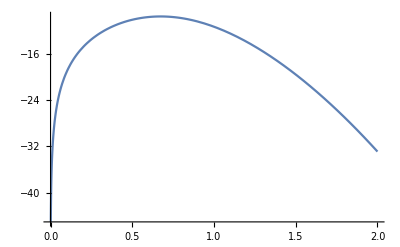

```mathematica
ruleβ = β->α-d;
rulezk=zk->4 α β Exp[-I k Γ];
f=√(zk^2+k^2)-k ArcSinh[k/zk]-α^2 Exp[-2I k Γ];
delta=(-√(zk^2+k^2)+k ArcSinh[k/zk]-α^2 Exp[-2I k Γ]/.rulezk/.{k->π/Γ})-(f/.rulezk/.{k->0});
Assuming[{α>0, β>0, Γ>0},Simplify@Normal@Series[delta, {Γ, 0, 1}]];
delta/.{Γ->10^-6,α->1000, β->999}//N;
temp = Assuming[{R>0, Γ>0},Simplify[delta/.{β->α}/.{α->R/(√Γ)}]]*Γ
Plot[temp, {R, 0, 2}]
```